```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
β[ω,0.001,1,0]
```

{{(0.+0.001 ⅈ)+ω,-1,0,0,0,0,0},{-1,(0.+0.001 ⅈ)+ω,-1,0,0,0,0},{0,-1,(0.+0.001 ⅈ)+ω,-1,0,0,0},{0,0,-1,(0.+0.001 ⅈ)+ω,-1,0,0},{0,0,0,-1,(0.+0.001 ⅈ)+ω,-1,0},{0,0,0,0,-1,(0.+0.001 ⅈ)+ω,-1},{0,0,0,0,0,-1,(0.+0.001 ⅈ)+ω}}

```mathematica
T2[t_]:=T2[t]={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:=T1[t]={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
T2[1]
```

{{1,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,1}}

```mathematica
T1[1]
```

{{0,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,0}}

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

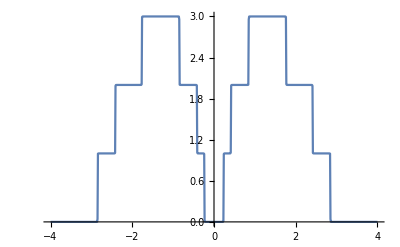
{306.168,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]]
```

```mathematica
ϕ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}],  μ9=RandomInteger[{6,11}],μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,5}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
k814[ω_,ϵ1_]:=k814[ω,ϵ1]=Append[{},Table[ϕ[ω,0.001,1,0,ϵ1],{i,1000}]]
```

```mathematica
ρ8[ω_,ϵ1_]:=Mean[k814[ω,ϵ1]]
```

```mathematica
Timing[ρ8[1.2,0.5]]
```

{5.67817,1.75181}

```mathematica
Timing[Export["/home/shardulmukim/8imp5.csv",Table[{ω,ρ8[ω,0.5]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
{2215.347259,"/home/shardulmukim/8imp5.csv"}
```

```mathematica
Export["8imp4.csv",Table[{ω,Mean[ρ8[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

8imp4.csv

```mathematica
"8imp.csv"
```

```mathematica
Export["8imp3.csv",Table[{ω,Mean[ρ8[ω,0.3]]},{ω,Range[0,4,0.01]}]]
```

8imp3.csv

```mathematica
"8imp.csv"
```

```mathematica
Export["8imp6.csv",Table[{ω,Mean[ρ8[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

8imp6.csv

```mathematica
"8imp.csv"
```

```mathematica
Export["8imp7.csv",Table[{ω,Mean[ρ8[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

8imp7.csv

```mathematica
"8imp.csv"
```

```mathematica
Export["8imp8.csv",Table[{ω,Mean[ρ8[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

8imp8.csv

```mathematica
"8imp.csv"
```

```mathematica
Export["8imp9.csv",Table[{ω,Mean[ρ8[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

8imp9.csv

```mathematica
Export["8imp1.csv",Table[{ω,Mean[ρ8[ω,1]]},{ω,Range[0,4,0.01]}]]
```

8imp1.csv

```mathematica
"8imp.csv"
```

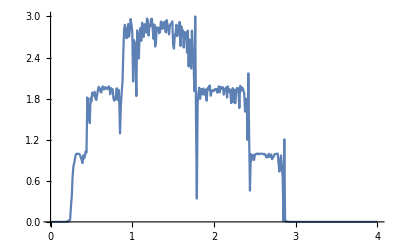

```mathematica
ListLinePlot[Table[{ω,ϕ[ω,0.001,1,0,0.2]},{ω,Range[0,4,0.01]}]]
```

```mathematica
μ1=RandomInteger[{1,7}]; μ2=RandomInteger[{1,7}]; μ3=RandomInteger[{1,7}]; μ4=RandomInteger[{1,7}]; μ5=RandomInteger[{1,7}]; μ6=RandomInteger[{1,7}]; μ7=RandomInteger[{1,7}]; μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[x]
```

```mathematica
test[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T1[t].SL[ω,δ,t,ϵ].T1[t]].x];Sl12:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T2[t].Sl11.T2[t]].x];(*Sl13:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T1[t].Sl12.T1[t]].x];Sl14:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T2[t].Sl13.T2[t]].x];Sl15:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T1[t].Sl14.T1[t]].x];Sl16:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T2[t].Sl15.T2[t]].x];Sl17:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T1[t].Sl16.T1[t]].x];Sl18:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T2[t].Sl17.T2[t]].x];Sl19:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T1[t].Sl18.T1[t]].x];Sl20:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T2[t].Sl19.T2[t]].x];Sl21:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T1[t].Sl20.T1[t]].x];Sl22:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T2[t].Sl21.T2[t]].x];Sl23:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T1[t].Sl22.T1[t]].x];Sl24:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T2[t].Sl23.T2[t]].x];Sl25:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T1[t].Sl24.T1[t]].x];Sl26:=Module[{x:=x=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}]},Inverse[IdentityMatrix[7]-x.T2[t].Sl25.T2[t]].x];*)Il1:=Inverse[IdentityMatrix[7]-Sl12.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl16;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl16.T1[t]].SR[ω,δ,t,ϵ];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
m1:= Table[{ω,test[ω,0.001,1,0,0.1]},{ω,Range[0,4,0.01]}]
```

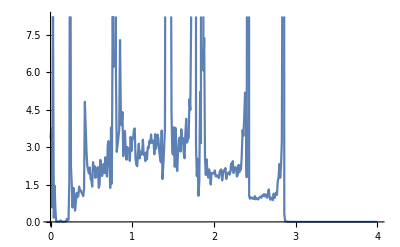

```mathematica
ListLinePlot[m1]
```

```mathematica
m2:= Table[{ω,test[ω,0.001,1,0,.2]},{ω,Range[0,4,0.01]}]
```

```mathematica
m3:= Table[{ω,test[ω,0.001,1,0,.3]},{ω,Range[0,4,0.01]}]
```

```mathematica
m4:= Table[{ω,test[ω,0.001,1,0,.4]},{ω,Range[0,4,0.01]}]
```

```mathematica
m5:= Table[{ω,test[ω,0.001,1,0,.5]},{ω,Range[0,4,0.01]}]
```

```mathematica
m6:= Table[{ω,test[ω,0.001,1,0,.6]},{ω,Range[0,4,0.01]}]
```

```mathematica
m7:= Table[{ω,test[ω,0.001,1,0,.7]},{ω,Range[0,4,0.01]}]
```

```mathematica
m8:= Table[{ω,test[ω,0.001,1,0,.8]},{ω,Range[0,4,0.01]}]
```

```mathematica
m9:= Table[{ω,test[ω,0.001,1,0,.9]},{ω,Range[0,4,0.01]}]
```

```mathematica
ρ33:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]- Import["/home/shardulmukim/8imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ34:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["/home/shardulmukim/8imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ35:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/8imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ36:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m6[[1;;400,2]]-Import["/home/shardulmukim/8imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ37:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m7[[1;;400,2]]- Import["/home/shardulmukim/8imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ38:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m8[[1;;400,2]]-Import["/home/shardulmukim/8imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ39:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m9[[1;;400,2]]-Import["/home/shardulmukim/8imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
A3:= {{3,ρ33},{4,ρ34},{5,ρ35},{6,ρ36},{7,ρ33},{8,ρ38},{9,ρ39}}
```

```mathematica
ListLinePlot[A3]
```

```mathematica
ϕ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
ϕ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
ϕ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
ϕ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
ϕ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
ϕ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
ϕ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
k77[ω_,ϵ1_]:=k77[ω,ϵ1]=Append[{},Table[ϕ7[ω,0.001,1,0,ϵ1],{i,150}]];
k76[ω_,ϵ1_]:=k76[ω,ϵ1]=Append[{},Table[ϕ6[ω,0.001,1,0,ϵ1],{i,150}]];
k75[ω_,ϵ1_]:=k75[ω,ϵ1]=Append[{},Table[ϕ5[ω,0.001,1,0,ϵ1],{i,150}]];
k74[ω_,ϵ1_]:=k74[ω,ϵ1]=Append[{},Table[ϕ4[ω,0.001,1,0,ϵ1],{i,150}]];
k73[ω_,ϵ1_]:=k73[ω,ϵ1]=Append[{},Table[ϕ3[ω,0.001,1,0,ϵ1],{i,150}]];
k72[ω_,ϵ1_]:=k72[ω,ϵ1]=Append[{},Table[ϕ2[ω,0.001,1,0,ϵ1],{i,150}]];
k71[ω_,ϵ1_]:=k71[ω,ϵ1]=Append[{},Table[ϕ1[ω,0.001,1,0,ϵ1],{i,150}]]
```

```mathematica
ρ7[ω_,ϵ1_]:=Join[Mean[k71[ω,ϵ1]],Mean[k72[ω,ϵ1]],Mean[k73[ω,ϵ1]],Mean[k74[ω,ϵ1]],Mean[k75[ω,ϵ1]],Mean[k76[ω,ϵ1]],Mean[k77[ω,ϵ1]]]
```

```mathematica
Timing[Mean[ρ7[1.5,0.5]]]
```

{12.2399,2.07211}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp5.csv",Table[{ω,Mean[ρ7[ω,0.5]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp5.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp4.csv",Table[{ω,Mean[ρ7[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp4.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp6.csv",Table[{ω,Mean[ρ7[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp6.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp7.csv",Table[{ω,Mean[ρ7[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp7.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp8.csv",Table[{ω,Mean[ρ7[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp8.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp9.csv",Table[{ω,Mean[ρ7[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp9.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp1.csv",Table[{ω,Mean[ρ7[ω,1]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/7imp1.csv

```mathematica
ξ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
ξ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
k614[ω_,ϵ1_]:=k614[ω,ϵ1]=Append[{},Table[ξ14[ω,0.001,1,0,ϵ1],{i,100}]];
k613[ω_,ϵ1_]:=k613[ω,ϵ1]=Append[{},Table[ξ13[ω,0.001,1,0,ϵ1],{i,100}]];
k612[ω_,ϵ1_]:=k612[ω,ϵ1]=Append[{},Table[ξ12[ω,0.001,1,0,ϵ1],{i,100}]];
k611[ω_,ϵ1_]:=k611[ω,ϵ1]=Append[{},Table[ξ11[ω,0.001,1,0,ϵ1],{i,100}]];
k610[ω_,ϵ1_]:=k610[ω,ϵ1]=Append[{},Table[ξ10[ω,0.001,1,0,ϵ1],{i,100}]];
k69[ω_,ϵ1_]:=k69[ω,ϵ1]=Append[{},Table[ξ9[ω,0.001,1,0,ϵ1],{i,100}]];
k68[ω_,ϵ1_]:=k68[ω,ϵ1]=Append[{},Table[ξ8[ω,0.001,1,0,ϵ1],{i,100}]];
k67[ω_,ϵ1_]:=k67[ω,ϵ1]=Append[{},Table[ξ7[ω,0.001,1,0,ϵ1],{i,100}]];
k66[ω_,ϵ1_]:=k66[ω,ϵ1]=Append[{},Table[ξ6[ω,0.001,1,0,ϵ1],{i,100}]];
k65[ω_,ϵ1_]:=k65[ω,ϵ1]=Append[{},Table[ξ5[ω,0.001,1,0,ϵ1],{i,100}]];
k64[ω_,ϵ1_]:=k64[ω,ϵ1]=Append[{},Table[ξ4[ω,0.001,1,0,ϵ1],{i,100}]];
k63[ω_,ϵ1_]:=k63[ω,ϵ1]=Append[{},Table[ξ3[ω,0.001,1,0,ϵ1],{i,100}]];
k62[ω_,ϵ1_]:=k62[ω,ϵ1]=Append[{},Table[ξ2[ω,0.001,1,0,ϵ1],{i,100}]];
k61[ω_,ϵ1_]:=k61[ω,ϵ1]=Append[{},Table[ξ1[ω,0.001,1,0,ϵ1],{i,100}]]
```

```mathematica
ρ6[ω_,ϵ1_]:=Join[Mean[k61[ω,ϵ1]],Mean[k62[ω,ϵ1]],Mean[k63[ω,ϵ1]],Mean[k64[ω,ϵ1]],Mean[k65[ω,ϵ1]],Mean[k66[ω,ϵ1]],Mean[k67[ω,ϵ1]],Mean[k68[ω,ϵ1]],Mean[k69[ω,ϵ1]],Mean[k610[ω,ϵ1]],Mean[k611[ω,ϵ1]],Mean[k613[ω,ϵ1]],Mean[k614[ω,ϵ1]]]
```

```mathematica
Mean[ρ6[0.5,0.5]]
```

1.3569

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp3.csv",Table[{ω,Mean[ρ6[ω,0.3]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp3.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp4.csv",Table[{ω,Mean[ρ6[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp4.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp6.csv",Table[{ω,Mean[ρ6[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp6.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp7.csv",Table[{ω,Mean[ρ6[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp7.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp8.csv",Table[{ω,Mean[ρ6[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp8.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp9.csv",Table[{ω,Mean[ρ6[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp9.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp1.csv",Table[{ω,Mean[ρ6[ω,1]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/6imp1.csv

```mathematica
α1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
α14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
Clear[k514,k513,k512,k511,k510,k59,k58,k57,k56,k55,k54,k53,k52,k51]
```

```mathematica
k514[ω_,ϵ1_]:=k514[ω,ϵ1]=Append[{},Table[α14[ω,0.001,1,0,ϵ1],{i,100}]];
k513[ω_,ϵ1_]:=k513[ω,ϵ1]=Append[{},Table[α13[ω,0.001,1,0,ϵ1],{i,100}]];
k512[ω_,ϵ1_]:=k512[ω,ϵ1]=Append[{},Table[α12[ω,0.001,1,0,ϵ1],{i,100}]];
k511[ω_,ϵ1_]:=k511[ω,ϵ1]=Append[{},Table[α11[ω,0.001,1,0,ϵ1],{i,100}]];
k510[ω_,ϵ1_]:=k510[ω,ϵ1]=Append[{},Table[α10[ω,0.001,1,0,ϵ1],{i,100}]];
k59[ω_,ϵ1_]:=k59[ω,ϵ1]=Append[{},Table[α9[ω,0.001,1,0,ϵ1],{i,100}]];
k58[ω_,ϵ1_]:=k58[ω,ϵ1]=Append[{},Table[α8[ω,0.001,1,0,ϵ1],{i,100}]];
k57[ω_,ϵ1_]:=k57[ω,ϵ1]=Append[{},Table[α7[ω,0.001,1,0,ϵ1],{i,100}]];
k56[ω_,ϵ1_]:=k56[ω,ϵ1]=Append[{},Table[α6[ω,0.001,1,0,ϵ1],{i,100}]];
k55[ω_,ϵ1_]:=k55[ω,ϵ1]=Append[{},Table[α5[ω,0.001,1,0,ϵ1],{i,100}]];
k54[ω_,ϵ1_]:=k54[ω,ϵ1]=Append[{},Table[α4[ω,0.001,1,0,ϵ1],{i,100}]];
k53[ω_,ϵ1_]:=k53[ω,ϵ1]=Append[{},Table[α3[ω,0.001,1,0,ϵ1],{i,100}]];
k52[ω_,ϵ1_]:=k52[ω,ϵ1]=Append[{},Table[α2[ω,0.001,1,0,ϵ1],{i,100}]];
k51[ω_,ϵ1_]:=k51[ω,ϵ1]=Append[{},Table[α1[ω,0.001,1,0,ϵ1],{i,100}]]
```

```mathematica
ρ5[ω_,ϵ1_]:=Join[Mean[k51[ω,ϵ1]],Mean[k52[ω,ϵ1]],Mean[k53[ω,ϵ1]],Mean[k54[ω,ϵ1]],Mean[k55[ω,ϵ1]],Mean[k56[ω,ϵ1]],Mean[k57[ω,ϵ1]],Mean[k58[ω,ϵ1]],Mean[k59[ω,ϵ1]],Mean[k510[ω,ϵ1]],Mean[k511[ω,ϵ1]],Mean[k513[ω,ϵ1]],Mean[k514[ω,ϵ1]]]
```

```mathematica
Timing[Mean[ρ5[0.4,0.7]]]
```

{7.63891,0.739931}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp3.csv",Table[{ω,Mean[ρ5[ω,0.3]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp4.csv",Table[{ω,Mean[ρ5[ω,0.4]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp5.csv",Table[{ω,Mean[ρ5[ω,0.5]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp6.csv",Table[{ω,Mean[ρ5[ω,0.6]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp7.csv",Table[{ω,Mean[ρ5[ω,0.7]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp8.csv",Table[{ω,Mean[ρ5[ω,0.8]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp9.csv",Table[{ω,Mean[ρ5[ω,0.9]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp1.csv",Table[{ω,Mean[ρ5[ω,1]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp3.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp4.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp5.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp6.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp7.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp8.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp9.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/5imp1.csv

```mathematica
χ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;`
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
χχ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
Clear[kk41,kk42,kk43,kk44,kk45,kk46,kk47,kk48,kk49,kk410,kk411,kk412,kk413,kk414]
```

```mathematica
k414[ω_,ϵ1_]:=k414[ω,ϵ1]=Append[{},Table[χ14[ω,0.001,1,0,ϵ1],{i,150}]];
k413[ω_,ϵ1_]:=k413[ω,ϵ1]=Append[{},Table[χ13[ω,0.001,1,0,ϵ1],{i,150}]];
k412[ω_,ϵ1_]:=k412[ω,ϵ1]=Append[{},Table[χ12[ω,0.001,1,0,ϵ1],{i,150}]];
k411[ω_,ϵ1_]:=k411[ω,ϵ1]=Append[{},Table[χ11[ω,0.001,1,0,ϵ1],{i,150}]];
k410[ω_,ϵ1_]:=k410[ω,ϵ1]=Append[{},Table[χ10[ω,0.001,1,0,ϵ1],{i,150}]];
k49[ω_,ϵ1_]:=k49[ω,ϵ1]=Append[{},Table[χ9[ω,0.001,1,0,ϵ1],{i,150}]];
k48[ω_,ϵ1_]:=k48[ω,ϵ1]=Append[{},Table[χ8[ω,0.001,1,0,ϵ1],{i,150}]];
k47[ω_,ϵ1_]:=k47[ω,ϵ1]=Append[{},Table[χ7[ω,0.001,1,0,ϵ1],{i,150}]];
k46[ω_,ϵ1_]:=k46[ω,ϵ1]=Append[{},Table[χ6[ω,0.001,1,0,ϵ1],{i,150}]];
k45[ω_,ϵ1_]:=k45[ω,ϵ1]=Append[{},Table[χ5[ω,0.001,1,0,ϵ1],{i,150}]];
k44[ω_,ϵ1_]:=k44[ω,ϵ1]=Append[{},Table[χ4[ω,0.001,1,0,ϵ1],{i,150}]];
k43[ω_,ϵ1_]:=k43[ω,ϵ1]=Append[{},Table[χ3[ω,0.001,1,0,ϵ1],{i,150}]];
k42[ω_,ϵ1_]:=k42[ω,ϵ1]=Append[{},Table[χ2[ω,0.001,1,0,ϵ1],{i,150}]];
k41[ω_,ϵ1_]:=k41[ω,ϵ1]=Append[{},Table[χ1[ω,0.001,1,0,ϵ1],{i,150}]];
kk414[ω_,ϵ1_]:=kk414[ω,ϵ1]=Append[{},Table[χχ14[ω,0.001,1,0,ϵ1],{i,150}]];
kk413[ω_,ϵ1_]:=kk413[ω,ϵ1]=Append[{},Table[χχ13[ω,0.001,1,0,ϵ1],{i,150}]];
kk412[ω_,ϵ1_]:=kk412[ω,ϵ1]=Append[{},Table[χχ12[ω,0.001,1,0,ϵ1],{i,150}]];
kk411[ω_,ϵ1_]:=kk411[ω,ϵ1]=Append[{},Table[χχ11[ω,0.001,1,0,ϵ1],{i,150}]];
kk410[ω_,ϵ1_]:=kk410[ω,ϵ1]=Append[{},Table[χχ10[ω,0.001,1,0,ϵ1],{i,150}]];
kk49[ω_,ϵ1_]:=kk49[ω,ϵ1]=Append[{},Table[χχ9[ω,0.001,1,0,ϵ1],{i,150}]];
kk48[ω_,ϵ1_]:=kk48[ω,ϵ1]=Append[{},Table[χχ8[ω,0.001,1,0,ϵ1],{i,150}]];
kk47[ω_,ϵ1_]:=kk47[ω,ϵ1]=Append[{},Table[χχ7[ω,0.001,1,0,ϵ1],{i,150}]];
kk46[ω_,ϵ1_]:=kk46[ω,ϵ1]=Append[{},Table[χχ6[ω,0.001,1,0,ϵ1],{i,150}]];
kk45[ω_,ϵ1_]:=kk45[ω,ϵ1]=Append[{},Table[χχ5[ω,0.001,1,0,ϵ1],{i,150}]];
kk44[ω_,ϵ1_]:=kk44[ω,ϵ1]=Append[{},Table[χχ4[ω,0.001,1,0,ϵ1],{i,150}]];
kk43[ω_,ϵ1_]:=kk43[ω,ϵ1]=Append[{},Table[χχ3[ω,0.001,1,0,ϵ1],{i,150}]];
kk42[ω_,ϵ1_]:=kk42[ω,ϵ1]=Append[{},Table[χχ2[ω,0.001,1,0,ϵ1],{i,150}]];
kk41[ω_,ϵ1_]:=kk41[ω,ϵ1]=Append[{},Table[χχ1[ω,0.001,1,0,ϵ1],{i,150}]]
```

```mathematica
ρ4[ω_,ϵ1_]:=Join[Mean[k41[ω,ϵ1]],Mean[k42[ω,ϵ1]],Mean[k43[ω,ϵ1]],Mean[k44[ω,ϵ1]],Mean[k45[ω,ϵ1]],Mean[k46[ω,ϵ1]],Mean[k47[ω,ϵ1]],Mean[k48[ω,ϵ1]],Mean[k49[ω,ϵ1]],Mean[k410[ω,ϵ1]],Mean[k411[ω,ϵ1]],Mean[k413[ω,ϵ1]],Mean[k414[ω,ϵ1]],Mean[kk41[ω,ϵ1]],Mean[kk42[ω,ϵ1]],Mean[kk43[ω,ϵ1]],Mean[kk44[ω,ϵ1]],Mean[kk45[ω,ϵ1]],Mean[kk46[ω,ϵ1]],Mean[kk47[ω,ϵ1]],Mean[kk48[ω,ϵ1]],Mean[kk49[ω,ϵ1]],Mean[kk410[ω,ϵ1]],Mean[kk411[ω,ϵ1]],Mean[kk413[ω,ϵ1]],Mean[kk414[ω,ϵ1]]]
```

```mathematica
Timing[Mean[ρ4[1.5,0.5]]]
```

{21.769,2.1685}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp3.csv",Table[{ω,Mean[ρ4[ω,0.3]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp3.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp4.csv",Table[{ω,Mean[ρ4[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp4.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp5.csv",Table[{ω,Mean[ρ4[ω,0.5]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp5.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp6.csv",Table[{ω,Mean[ρ4[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp6.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp7.csv",Table[{ω,Mean[ρ4[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp7.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp8.csv",Table[{ω,Mean[ρ4[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp8.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp9.csv",Table[{ω,Mean[ρ4[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp9.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp1.csv",Table[{ω,Mean[ρ4[ω,1]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/4imp1.csv

```mathematica
σ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
σ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
γ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
k314[ω_,ϵ1_]:=k314[ω,ϵ1]=Append[{},Table[σ14[ω,0.001,1,0,ϵ1],{i,100}]];
k313[ω_,ϵ1_]:=k313[ω,ϵ1]=Append[{},Table[σ13[ω,0.001,1,0,ϵ1],{i,100}]];
k312[ω_,ϵ1_]:=k312[ω,ϵ1]=Append[{},Table[σ12[ω,0.001,1,0,ϵ1],{i,100}]];
k311[ω_,ϵ1_]:=k311[ω,ϵ1]=Append[{},Table[σ11[ω,0.001,1,0,ϵ1],{i,100}]];
k310[ω_,ϵ1_]:=k310[ω,ϵ1]=Append[{},Table[σ10[ω,0.001,1,0,ϵ1],{i,100}]];
k39[ω_,ϵ1_]:=k39[ω,ϵ1]=Append[{},Table[σ9[ω,0.001,1,0,ϵ1],{i,100}]];
k38[ω_,ϵ1_]:=k38[ω,ϵ1]=Append[{},Table[σ8[ω,0.001,1,0,ϵ1],{i,100}]];
k37[ω_,ϵ1_]:=k37[ω,ϵ1]=Append[{},Table[σ7[ω,0.001,1,0,ϵ1],{i,100}]];
k36[ω_,ϵ1_]:=k36[ω,ϵ1]=Append[{},Table[σ6[ω,0.001,1,0,ϵ1],{i,100}]];
k35[ω_,ϵ1_]:=k35[ω,ϵ1]=Append[{},Table[σ5[ω,0.001,1,0,ϵ1],{i,100}]];
k34[ω_,ϵ1_]:=k34[ω,ϵ1]=Append[{},Table[σ4[ω,0.001,1,0,ϵ1],{i,100}]];
k33[ω_,ϵ1_]:=k33[ω,ϵ1]=Append[{},Table[σ3[ω,0.001,1,0,ϵ1],{i,100}]];
k32[ω_,ϵ1_]:=k32[ω,ϵ1]=Append[{},Table[σ2[ω,0.001,1,0,ϵ1],{i,100}]];
k31[ω_,ϵ1_]:=k31[ω,ϵ1]=Append[{},Table[σ1[ω,0.001,1,0,ϵ1],{i,100}]];kk314[ω_,ϵ1_]:=kk314[ω,ϵ1]=Append[{},Table[γ14[ω,0.001,1,0,ϵ1],{i,100}]];
kk313[ω_,ϵ1_]:=kk313[ω,ϵ1]=Append[{},Table[γ13[ω,0.001,1,0,ϵ1],{i,100}]];
kk312[ω_,ϵ1_]:=kk312[ω,ϵ1]=Append[{},Table[γ12[ω,0.001,1,0,ϵ1],{i,100}]];
kk311[ω_,ϵ1_]:=kk311[ω,ϵ1]=Append[{},Table[γ11[ω,0.001,1,0,ϵ1],{i,100}]];
kk310[ω_,ϵ1_]:=kk310[ω,ϵ1]=Append[{},Table[γ10[ω,0.001,1,0,ϵ1],{i,100}]];
kk39[ω_,ϵ1_]:=kk39[ω,ϵ1]=Append[{},Table[γ9[ω,0.001,1,0,ϵ1],{i,100}]];
kk38[ω_,ϵ1_]:=kk38[ω,ϵ1]=Append[{},Table[γ8[ω,0.001,1,0,ϵ1],{i,100}]];
kk37[ω_,ϵ1_]:=kk37[ω,ϵ1]=Append[{},Table[γ7[ω,0.001,1,0,ϵ1],{i,100}]];
kk36[ω_,ϵ1_]:=kk36[ω,ϵ1]=Append[{},Table[γ6[ω,0.001,1,0,ϵ1],{i,100}]];
kk35[ω_,ϵ1_]:=kk35[ω,ϵ1]=Append[{},Table[γ5[ω,0.001,1,0,ϵ1],{i,100}]];
kk34[ω_,ϵ1_]:=kk34[ω,ϵ1]=Append[{},Table[γ4[ω,0.001,1,0,ϵ1],{i,100}]];
kk33[ω_,ϵ1_]:=kk33[ω,ϵ1]=Append[{},Table[γ3[ω,0.001,1,0,ϵ1],{i,100}]];
kk32[ω_,ϵ1_]:=kk32[ω,ϵ1]=Append[{},Table[γ2[ω,0.001,1,0,ϵ1],{i,100}]];
kk31[ω_,ϵ1_]:=kk31[ω,ϵ1]=Append[{},Table[γ1[ω,0.001,1,0,ϵ1],{i,100}]]
```

```mathematica
ρ3[ω_,ϵ1_]:=Join[Mean[k31[ω,ϵ1]],Mean[k32[ω,ϵ1]],Mean[k33[ω,ϵ1]],Mean[k34[ω,ϵ1]],Mean[k35[ω,ϵ1]],Mean[k36[ω,ϵ1]],Mean[k37[ω,ϵ1]],Mean[k38[ω,ϵ1]],Mean[k39[ω,ϵ1]],Mean[k310[ω,ϵ1]],Mean[k311[ω,ϵ1]],Mean[k313[ω,ϵ1]],Mean[k314[ω,ϵ1]],Mean[kk31[ω,ϵ1]],Mean[kk32[ω,ϵ1]],Mean[kk33[ω,ϵ1]],Mean[kk34[ω,ϵ1]],Mean[kk35[ω,ϵ1]],Mean[kk36[ω,ϵ1]],Mean[kk37[ω,ϵ1]],Mean[kk38[ω,ϵ1]],Mean[kk39[ω,ϵ1]],Mean[kk310[ω,ϵ1]],Mean[kk311[ω,ϵ1]],Mean[kk313[ω,ϵ1]],Mean[kk314[ω,ϵ1]]]
```

```mathematica
Timing[Mean[ρ3[1,0.5]]]
```

{14.7945,2.64896}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp3.csv",Table[{ω,Mean[ρ3[ω,0.3]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp4.csv",Table[{ω,Mean[ρ3[ω,0.4]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp6.csv",Table[{ω,Mean[ρ3[ω,0.6]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp7.csv",Table[{ω,Mean[ρ3[ω,0.7]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp8.csv",Table[{ω,Mean[ρ3[ω,0.8]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp9.csv",Table[{ω,Mean[ρ3[ω,0.9]]},{ω,Range[0,4,0.01]}]]
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp1.csv",Table[{ω,Mean[ρ3[ω,1]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp3.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp4.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp6.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp7.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp8.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp9.csv

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/3imp1.csv

```mathematica
ζ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
ζ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
ζ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
ζ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
ζ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
ζ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
ζ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Sl19:=Inverse[IdentityMatrix[7]-imp1.T1[t].Sl18.T1[t]].imp1;
Sl20:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl19.T2[t]].imp2;
Sl21:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl20.T1[t]].imp3;
Sl22:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl21.T2[t]].imp4;
Sl23:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl22.T1[t]].imp5;
Sl24:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl23.T2[t]].imp6;
Sl25:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl24.T1[t]].imp7;
Sl26:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl25.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl26.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl26;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl26.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
k27[ω_,ϵ1_]:=k27[ω,ϵ1]=Append[{},Table[ζ7[ω,0.001,1,0,ϵ1],{i,150}]];
k26[ω_,ϵ1_]:=k26[ω,ϵ1]=Append[{},Table[ζ6[ω,0.001,1,0,ϵ1],{i,150}]];
k25[ω_,ϵ1_]:=k25[ω,ϵ1]=Append[{},Table[ζ5[ω,0.001,1,0,ϵ1],{i,150}]];
k24[ω_,ϵ1_]:=k24[ω,ϵ1]=Append[{},Table[ζ4[ω,0.001,1,0,ϵ1],{i,150}]];
k23[ω_,ϵ1_]:=k23[ω,ϵ1]=Append[{},Table[ζ3[ω,0.001,1,0,ϵ1],{i,150}]];
k22[ω_,ϵ1_]:=k22[ω,ϵ1]=Append[{},Table[ζ2[ω,0.001,1,0,ϵ1],{i,150}]];
k21[ω_,ϵ1_]:=k21[ω,ϵ1]=Append[{},Table[ζ1[ω,0.001,1,0,ϵ1],{i,150}]]
```

```mathematica
ρ2[ω_,ϵ1_]:=Join[Mean[k21[ω,ϵ1]],Mean[k22[ω,ϵ1]],Mean[k23[ω,ϵ1]],Mean[k24[ω,ϵ1]],Mean[k25[ω,ϵ1]],Mean[k26[ω,ϵ1]],Mean[k27[ω,ϵ1]]]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp3.csv",Table[{ω,Mean[ρ2[ω,0.3]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp3.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp4.csv",Table[{ω,Mean[ρ2[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp4.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp6.csv",Table[{ω,Mean[ρ2[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp6.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp7.csv",Table[{ω,Mean[ρ2[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp7.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp8.csv",Table[{ω,Mean[ρ2[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp8.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp9.csv",Table[{ω,Mean[ρ2[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp9.csv

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp1.csv",Table[{ω,Mean[ρ2[ω,1]]},{ω,Range[0,4,0.01]}]]
```

/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp1.csv